```mathematica
<<Local`QFTToolKit`
QCDBaseIndices
DefineDottedIndices
Put[SaveFile=NBname["stub"]<>".out"]
```

{{0,1,2,3},{field,{1,2,3,4}},{feyn,{1,2,3,4,5}},{space,{1,2,3}},{timespace,{0,1}},{groupR,{1,2,3}},{gaugeG,{1,2,3,4,5,6,7,8}},{color,{1,2,3}},{flavor,{1,2,3,4,5,6}},{family,{1,2,3}}}

```mathematica
DefineTensorShortcuts[{{η,t,δ,ε,λ,D,F,U,M,H,g,τ,v,H,m,μ,u,Q},1},
{{y,U,u,ψ,V,h,H},2},
{{σ,λ,T},3}
]
```

Lecture 24 Oct 2011 notes -- SUSY, Higgs, MSSM,  super particle search

```mathematica
PR1["2 component Higgs: ",NL,
(subH={Hd[1]->{{(vd[1]+hd[1]/√2)Exp[(I/(vd[1] √2))(-Cos[β]Gu[0]+Sin[β]A)]},{Sin[β]Hu["-"]-Cos[β]Gu["-"]}},
Hd[2]->{{Cos[β]Hu["+"]+Sin[β]Gu["+"]},{(vd[2]+hd[2]/√2)Exp[(I/(vd[2] √2))(Sin[β]Gu[0]+Cos[β]A)]},{Sin[β]Hu["-"]-Cos[β]Gu["-"]}}})//MatrixForms,NL,



"What is mass of higgs?",NL,
"Notes: ",NL,
{{hd[1],hd[2]},"mix to",{h,H},{{hd[1]},{hd[2]}}->{{Cos[α],-Sin[α]},{Sin[α],Cos[α]}}**{{H},{h}}}//MatrixForms,NL,
md[h]<Md[Z]Abs[Cos[2 β]]," has been excluded below 100 Gev without the inclusion of radiative corrections for the top ",δd[top],NL,
"mass of top unexpectedly heavy and coupling strong.",NL,
"Review of some relationships:",NL,
(subM={
Md[A]^2->μd[1]^2+μd[2]^2,
Md[Z]^2->(g^2+g'^2)/2(vd[1]^2+vd[2]^2),
Md[Z]^2->(μd[1]^2-μd[2]^2Tan[β]^2)/(Tan[β]^2-1),
Md[Hu["+"]]^2->Md[A]^2+Md[W]^2,
μd[1]^2->μ^2+md[Hd[1]]^2,
μd[2]^2->μ^2+md[Hd[2]]^2,
Sin[2β]->2μd[3]^2/(μd[1]^2+μd[2]^2),
Tan[β]->vd[2]/vd[1]
}
)//Column
]
```

2 component Higgs: 
{H_1^1→(ⅇ^((ⅈ (A Sin[β]-Cos[β] G_0^0))/(√2 v_1^1)) (h_1^1/(√2)+v_1^1)
-Cos[β] G_-^-+Sin[β] H_-^-),H_2^2→(Sin[β] G_+^++Cos[β] H_+^+
ⅇ^((ⅈ (A Cos[β]+Sin[β] G_0^0))/(√2 v_2^2)) (h_2^2/(√2)+v_2^2)
-Cos[β] G_-^-+Sin[β] H_-^-)}
What is mass of higgs?
Notes: 
{{h_1^1,h_2^2},mix to,{h,H},(h_1^1
h_2^2)→(Cos[α] | -Sin[α]
Sin[α] | Cos[α])**(H
h)}
m_h^h<Abs[Cos[2 β]] M_Z^Z has been excluded below 100 Gev without the inclusion of radiative corrections for the top δ_top^top
mass of top unexpectedly heavy and coupling strong.
Review of some relationships:
(M_A^A)^2→(μ_1^1)^2+(μ_2^2)^2
(M_Z^Z)^2→1/2 ((v_1^1)^2+(v_2^2)^2) (g^2+(g')^2)
(M_Z^Z)^2→((μ_1^1)^2-Tan[β]^2 (μ_2^2)^2)/(-1+Tan[β]^2)
(M_(H_+^+)^(H_+^+))^2→(M_A^A)^2+(M_W^W)^2
(μ_1^1)^2→μ^2+(m_(H_1^1)^(H_1^1))^2
(μ_2^2)^2→μ^2+(m_(H_2^2)^(H_2^2))^2
Sin[2 β]→(2 (μ_3^3)^2)/((μ_1^1)^2+(μ_2^2)^2)
Tan[β]→v_2^2/v_1^1

A Md[A]-Md[{h,H+,}] plot was presented for two different values of Tan[β].  Take mass formulas from lecture 2011.10.14: {(M_(H_+^+)^(H_+^+))^2==(M_A^A)^2+(M_W^W)^2}

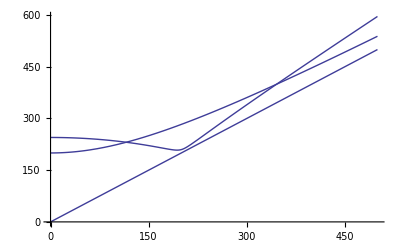

```mathematica
PR1["A Md[A]-Md[{h,H+,}] plot was presented for two different values of Tan[β].  Take mass formulas from lecture 2011.10.14: ",
{Md[Hd["+"]]^2==Md[A]^2+Md[W]^2
}
]
Plot[({Md[A],
√(Md[A]^2+Md[W]^2),
√(1/2(Md[Z]^2+Md[A]^2)+√((Md[Z]^2+Md[A]^2)^2-4 Md[Z]^2 Md[A]^2 Cos[2 β]^2))
}//.{Md[W]->200,Md[Z]->200,β->ArcTan[40.]}),{Md[A],0,500}]
```

General graphic definitions for array points and lines.

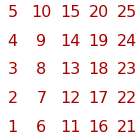

{{{0,0},{0,1},{0,2},{0,3},{0,4},{1,0},{1,1},{1,2},{1,3},{1,4},{2,0},{2,1},{2,2},{2,3},{2,4},{3,0},{3,1},{3,2},{3,3},{3,4},{4,0},{4,1},{4,2},{4,3},{4,4}},{}}

```mathematica
GraphicPointLines[5,5,{}]
```

```mathematica
PR1["To get h heavy: ",yield,μd[1]^2," large ⟶ decouples Hd[1]",Yield,
V[Hd[2]]->μd[2]^2 SuperDagger[hdu[2,0]].hdu[2,0]+(g^2+g'^2)/8(SuperDagger[hdu[2,0]].hdu[2,0])^2,imply,
md[h]^2->4((g^2+g'^2)/8)v^2->4 λ v^2,NL,
"Need extra contribution. ",NL,
{gd[3],gd[t->top]}," are large and good for radiative corrections, but ",gd[3]," does not couple to color so ",gd[t]," is only available.  Look at Yukawa coupling ",tmpY=W-> Qd[3].yd[t].Ud[3].Hd[3]," where ",Qd[3]->T[q̃,"d",{3}]+θ qd[3]," with diagrams ",CR["Need diagrams"]
]
```

To get h heavy:  ⟶ (μ_1^1)^2 large ⟶ decouples Hd[1]
→ V[H_2^2]→(h_20^20)^†.h_20^20 (μ_2^2)^2+1/8 ((h_20^20)^†.h_20^20)^2 (g^2+(g')^2) ⇒ (m_h^h)^2→1/2 v^2 (g^2+(g')^2)→4 v^2 λ
Need extra contribution. 
{g_3^3,g_(t→top)^(t→top)} are large and good for radiative corrections, but g_3^3 does not couple to color so g_t^t is only available.  Look at Yukawa coupling W→Q_3^3.y_t^t.U_3^3.H_3^3 where Q_3^3→θ q_3^3+(q̃)_3^3 with diagrams Need diagrams

```mathematica
PR1["If SUSY conserved then superpartner masses are equal and the radiative corrections cancel.  Some sort of dead lock where one need the mass of the top quark to calculate VEV but needs VEV to calculate corrections to the potential.
Colewan-Weinberg Theorem (1970): Suppose the potential is a function of {i,1,n[higgs]} higgs masses. ",
V[H]->fn[md[i][H],{i,n[higgs]}],Imply,
tmpδV=δV[H]->3/(64 π^2)xSum[(-1)^Fd[i] gd[i](md[i][H])^4 Log[(md[i][H]^2)/μ^2],{i}],
" where ",{3->"color factor",μ->"renormalization scale taken near largest md[i][H]",Fd[i]->"Fermion count",gd[i]->{"Dirac fermions"->4,"Complex scalar"->2}}//Column,NL,
"Example for the above Yukawa potential ",tmpY,"  using",NL,
(tmpm={md[t]->yd[t].H, md[T[q̃,"d",{3}]]->√((yd[t].H)^2+md[Qd[3]]^2),md[T[ũ,"d",{3}]]->√((yd[t].H)^2+md[ud[3]]^2)})//Column,
" where ",{md[Qd[3]],md[T[ũ,"d",{3}]]}," are the SSB parameters."
];
```

If SUSY conserved then superpartner masses are equal and the radiative corrections cancel.  Some sort of dead lock where one need the mass of the top quark to calculate VEV but needs VEV to calculate corrections to the potential.
Colewan-Weinberg Theorem (1970): Suppose the potential is a function of {i,1,n[higgs]} higgs masses. V[H]→fn[m_i^i[H],{i,n[higgs]}]
⇒ δV[H]→(3 UnderBar[∑]_{i}[(-1)^(F_i^i) Log[((m_i^i[H])^2)/μ^2] g_i^i (m_i^i[H])^4])/(64 π^2) where 3→color factor
μ→renormalization scale taken near largest md[i][H]
F_i^i→Fermion count
g_i^i→{Dirac fermions→4,Complex scalar→2}
Example for the above Yukawa potential W→Q_3^3.y_t^t.U_3^3.H_3^3  using
m_t^t→y_t^t.H
m_((q̃)_3^3)^((q̃)_3^3)→√((y_t^t.H)^2+(m_(Q_3^3)^(Q_3^3))^2)
m_((ũ)_3^3)^((ũ)_3^3)→√((y_t^t.H)^2+(m_(u_3^3)^(u_3^3))^2) where {m_(Q_3^3)^(Q_3^3),m_((ũ)_3^3)^((ũ)_3^3)} are the SSB parameters.

```mathematica
PR1["Then mapping ",
sub=MapIndexed[Rule[md[#2[[1]]][H],#1[[2]]]&,tmpm],and,
sub1={Fd[1]->1,Fd[2]->0,Fd[3]->0,gd[1]->4,gd[2]->2,gd[3]->2},NL,
tmp=tmpδV/.xSum[a_,b_]:>Sum[a,{i,3}],Yield,
tmp=tmp/.sub/.sub1,Yield,
tmp=tmp//Expand;Yield,
tmp=Collect[tmp,{yd[t].H},Simplify[#]/.a_ Log[b_]->Log[b^a]//.Log[a_]+Log[b_]->Log[a b]&],NL,
"It appears that in lecture it is assumed that ",sub={md[Qd[3]]|md[ud[3]]->md[t̃]},Imply,
tmpδV1=tmp/.sub/.Log[a_^2/b_^4]->2Log[a/b^2]//Simplify,NL,
"The Log[] in the quadratic term can be expanded in powers of H^(2  n) indicating that it includes higher order higgs interactions."
]
```

Then mapping {m_1^1[H]→y_t^t.H,m_2^2[H]→√((y_t^t.H)^2+(m_(Q_3^3)^(Q_3^3))^2),m_3^3[H]→√((y_t^t.H)^2+(m_(u_3^3)^(u_3^3))^2)} and {F_1^1→1,F_2^2→0,F_3^3→0,g_1^1→4,g_2^2→2,g_3^3→2}
δV[H]→(3 ((-1)^(F_1^1) Log[((m_1^1[H])^2)/μ^2] g_1^1 (m_1^1[H])^4+(-1)^(F_2^2) Log[((m_2^2[H])^2)/μ^2] g_2^2 (m_2^2[H])^4+(-1)^(F_3^3) Log[((m_3^3[H])^2)/μ^2] g_3^3 (m_3^3[H])^4))/(64 π^2)
→ δV[H]→(3 (-4 (y_t^t.H)^4 Log[((y_t^t.H)^2)/μ^2]+2 Log[((y_t^t.H)^2+(m_(Q_3^3)^(Q_3^3))^2)/μ^2] ((y_t^t.H)^2+(m_(Q_3^3)^(Q_3^3))^2)^2+2 Log[((y_t^t.H)^2+(m_(u_3^3)^(u_3^3))^2)/μ^2] ((y_t^t.H)^2+(m_(u_3^3)^(u_3^3))^2)^2))/(64 π^2)
→ 
→ δV[H]→(3 (y_t^t.H)^4 Log[(((y_t^t.H)^2+(m_(Q_3^3)^(Q_3^3))^2) ((y_t^t.H)^2+(m_(u_3^3)^(u_3^3))^2))/((y_t^t.H)^4)])/(32 π^2)+(3 (y_t^t.H)^2 Log[(((y_t^t.H)^2+(m_(Q_3^3)^(Q_3^3))^2)/μ^2)^((m_(Q_3^3)^(Q_3^3))^2) (((y_t^t.H)^2+(m_(u_3^3)^(u_3^3))^2)/μ^2)^((m_(u_3^3)^(u_3^3))^2)])/(16 π^2)+(3 Log[(((y_t^t.H)^2+(m_(Q_3^3)^(Q_3^3))^2)/μ^2)^((m_(Q_3^3)^(Q_3^3))^4) (((y_t^t.H)^2+(m_(u_3^3)^(u_3^3))^2)/μ^2)^((m_(u_3^3)^(u_3^3))^4)])/(32 π^2)
It appears that in lecture it is assumed that {m_(Q_3^3)^(Q_3^3)|m_(u_3^3)^(u_3^3)→m_(t̃)^(t̃)}
⇒ δV[H]→(3 (2 (y_t^t.H)^2 Log[(((y_t^t.H)^2+(m_(t̃)^(t̃))^2)/μ^2)^(2 (m_(t̃)^(t̃))^2)]+Log[(((y_t^t.H)^2+(m_(t̃)^(t̃))^2)/μ^2)^(2 (m_(t̃)^(t̃))^4)]+2 (y_t^t.H)^4 Log[1+((m_(t̃)^(t̃))^2)/((y_t^t.H)^2)]))/(32 π^2)
The Log[] in the quadratic term can be expanded in powers of H^(2  n) indicating that it includes higher order higgs interactions.

```mathematica
PR1["If we choose ",
tmp=ExtractPattern[tmpδV1,Log[a_^b_]][[1,1,1]]->1,yield,
sub=RuleX[tmp,μ],Imply,
tmp=tmpδV1/.sub,NL,
"The Log[] term can be expanded: ",
tmp=tmp/.Log[1+a_]->Log[a]+Log[1+1/a],yield,
tmp=tmp//Expand,Yield,
tmp=tmp/.Log[1+a_]:>(Normal[Series[Log[1+x],{x,0,3}]]/.x->a),
" shows that this expression includes higher order H terms."
]
```

If we choose ((y_t^t.H)^2+(m_(t̃)^(t̃))^2)/μ^2→1 ⟶ {μ→-√((y_t^t.H)^2+(m_(t̃)^(t̃))^2)}
⇒ δV[H]→(3 (y_t^t.H)^4 Log[1+((m_(t̃)^(t̃))^2)/((y_t^t.H)^2)])/(16 π^2)
The Log[] term can be expanded: δV[H]→(3 (y_t^t.H)^4 (Log[1+((y_t^t.H)^2)/((m_(t̃)^(t̃))^2)]+Log[((m_(t̃)^(t̃))^2)/((y_t^t.H)^2)]))/(16 π^2) ⟶ δV[H]→(3 (y_t^t.H)^4 Log[1+((y_t^t.H)^2)/((m_(t̃)^(t̃))^2)])/(16 π^2)+(3 (y_t^t.H)^4 Log[((m_(t̃)^(t̃))^2)/((y_t^t.H)^2)])/(16 π^2)
→ δV[H]→(3 (y_t^t.H)^4 Log[((m_(t̃)^(t̃))^2)/((y_t^t.H)^2)])/(16 π^2)+(3 (y_t^t.H)^4 (((y_t^t.H)^6)/(3 (m_(t̃)^(t̃))^6)-((y_t^t.H)^4)/(2 (m_(t̃)^(t̃))^4)+((y_t^t.H)^2)/((m_(t̃)^(t̃))^2)))/(16 π^2) shows that this expression includes higher order H terms.